```mathematica
passesRaw = Import["/Users/herwig/University/Master/Courses/HS23/Sport Networks/ice-hockey/2022-02-16 Switzerland at Finland passes.csv"];
```

```mathematica
passesG = Select[passesRaw, #[[3]]>1&];
vertices = Labeled[#[[1]],#[[1]]]&/@passesG;
edges = Labeled[#[[1]]<->#[[2]],#[[3]]]& /@ passesG;
passesG = Graph[vertices, edges];
```

6

18

{7,7,6,7,6,3}

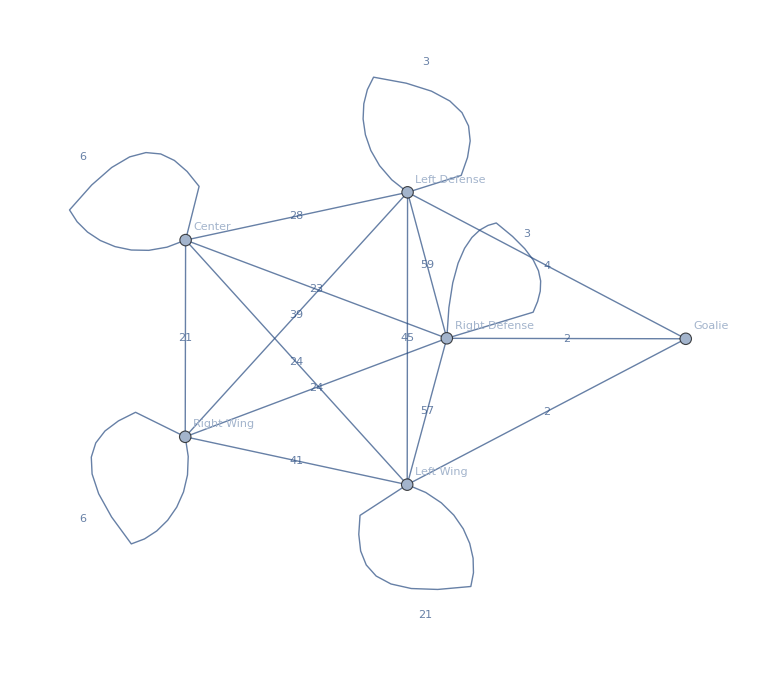

```mathematica
Print[VertexCount[passesG]];
Print[EdgeCount[passesG]];
Print[VertexDegree[passesG]];
GraphPlot[passesG]
```